2.23538×10^-44 ⅇ^Re[(0.-78539.8 ⅈ) √((0.16064+T)/T)-(0.+78539.8 ⅈ) √((0.161231+T)/T)] √(1/((1+0.16064/T) √(1+0.161231/T))) Abs[(1. ⅇ^((0.+157080. ⅈ) √((0.16064+T)/T))-1. ⅇ^((0.+157080. ⅈ) √((0.161231+T)/T))) T (1. √((0.16064+T)/T)+1. √((0.161231+T)/T))]

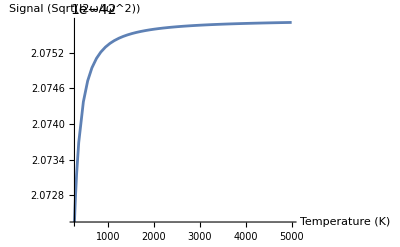

```mathematica
Clear["`*"]
EExt=100;
cl=299792458;(*Meter per second*)
ϵ0=8.8541878188*10^-12;
χ3=6419*10^-54;
L=0.01;

λ1 = 0.8;(*micro meter*)
λ2 = λ1/2;(*micro meter*)
ω = 2π(cl)/(λ1*10^(-6));
ω2= ω*2;

p0=1000;(*mbar*)
p=1013;(*https://www.wolframalpha.com/input?i=pressure+atmosphere+bar*)
T0=273;(*Kelvin*)
B1=39209.95*10^-8;(*um^2*)
B2=18806.48*10^-8;
C1=1146.24*10^-6;
C2=13.476*10^-6;
n=Sqrt[1+(p/p0)(T0/T)(B1 λ^2/(λ^2-C1)+B2 λ^2/(λ^2-C2))];
nω=n/.{λ->λ1};
n2ω=n/.{λ->λ2};

Δk=2nω ω/cl-n2ω 2ω/cl;
c=Sqrt[(9/2)(ω^2/(ϵ0 cl^3 nω^2 n2ω))]Abs[χ3];
Signal = c Abs[Integrate[EExt Exp[-I Δk z],{z,-0.5L, 0.5L}]](*Negeer hier die Rayleigh length, boeit dat?*)
Plot[Signal, {T, 273, 5000},AxesLabel->{"Temperature (K)", "Signal (Sqrt(I2ω/Iω^2))"},PlotRange->Full]
```